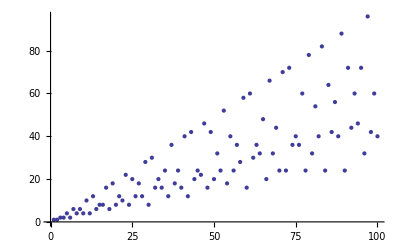

```mathematica
Table[EulerPhi[x], {x, 1, 100}];
ListPlot[%]
```

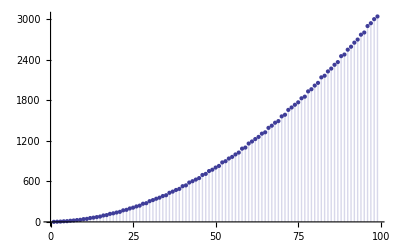

```mathematica
tot=0;
Table[(tot=tot+EulerPhi[k];tot),{k,2,100}];
ListPlot[%, Filling -> Axis]
```

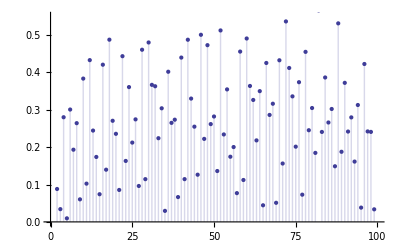

```mathematica
tot=0;
Table[((tot=tot+EulerPhi[k];tot)-3 k^2/Pi^2)/k,{k,2,100}];
ListPlot[%, Filling -> Axis, PlotRange -> {{0,100},{0,0.55}}]
```

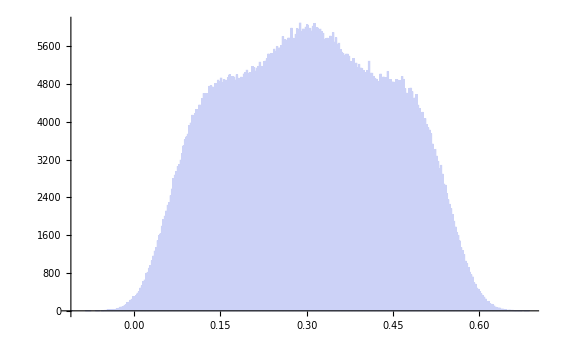

```mathematica
Histogram[(tot=0;Table[((tot=tot+EulerPhi[k];tot)-3 k^2/Pi^2)/k,{k,2,1000000}]),{0.0025}]
```

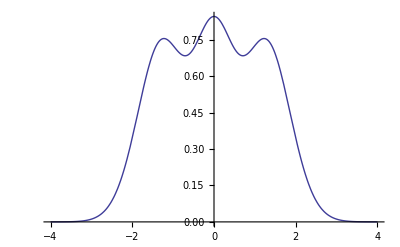

```mathematica
Plot[Sum[1/Sqrt[Pi]HermiteH[k,x]^2/2^k/k!,{k,0,2}]E^(-x^2),{x, -4,4}]
```